LQR增益矩阵 K = {{3.15345+0. ⅈ,4.47214+0. ⅈ}}

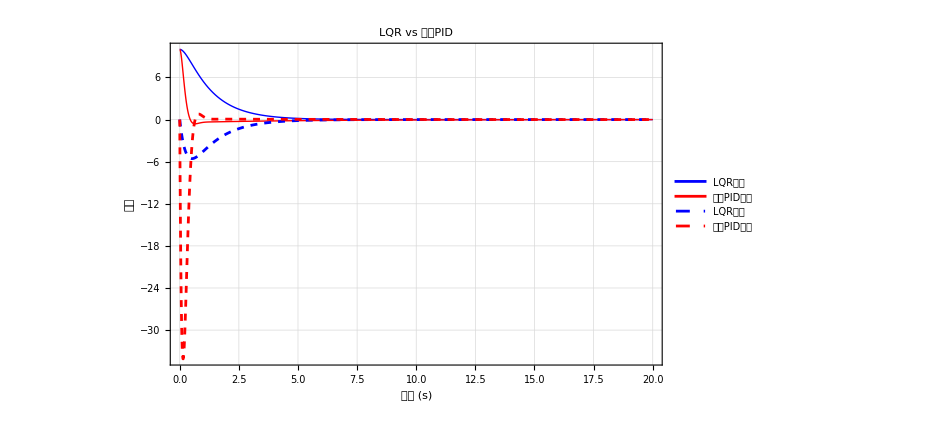

```mathematica
ClearAll["Global`*"]

(*系统参数-双积分器系统*)
(*x1'=x2,x2'=u*)
{a,b,c,d}={({{0, 0}, {1, 0}}),({{1}, {0}}),({{1, 0}, {0, 1}}),({{0}, {0}})};

(*LQR参数*)
{q, r} = {({{1, 0}, {0, 20}}), {{1}}};

(*串级PID参数*)
Kp1=10;   (*外环比例增益*)
Ki1=2;    (*外环积分增益*)
Kd1=1;    (*外环微分增益*)
Kp2=6;    (*内环比例增益*)
Ki2=0;    (*内环积分增益*)

(*仿真参数*)
reference=0;       (*参考输入-调节到原点*)
initialPos=10;     (*初始位置*)
initialVel=0;      (*初始速度*)
tmax=20;           (*仿真时间*)

(* ==========LQR控制器==========*)
ssm=StateSpaceModel[{a,b,c,d}];
sspec=<|"InputModel"->ssm,"FeedbackInputs"->1|>;
K=LQRegulatorGains[sspec,{q,r}]//N;

(*手动构建闭环系统确保正确的负反馈*)
AK=a-b.K;  (*闭环系统矩阵*)
closedSys=StateSpaceModel[{AK,b,c,d}];
x0={initialPos,initialVel};

(*LQR响应计算*)
lqrSol=NDSolve[{x1'[t]==x2[t],x2'[t]==-K[[1,1]]*x1[t]-K[[1,2]]*x2[t],(*负反馈控制*)x1[0]==initialPos,x2[0]==initialVel},{x1,x2},{t,0,tmax}];

lqrPosition=x1[t]/. lqrSol[[1]];
lqrVelocity=x2[t]/. lqrSol[[1]];

(* ==========串级PID控制器==========*)
cascadePID[kp1_,ki1_,kd1_,kp2_,ki2_,ref_,x0pos_,x0vel_,tmax_]:=Module[{sol},sol=NDSolve[{(*系统动态方程*)x1'[t]==x2[t],x2'[t]==u[t],(*外环PID控制器*)(*位置误差*)e1[t]==ref-x1[t],(*外环积分项*)int1'[t]==e1[t],(*外环输出（内环参考速度）-微分项是-x2[t]因为de1/dt=-dx1/dt=-x2[t]*)velRef[t]==kp1*e1[t]+ki1*int1[t]+kd1*(-x2[t]),(*内环PID控制器*)(*速度误差*)e2[t]==velRef[t]-x2[t],(*内环积分项*)int2'[t]==e2[t],(*内环输出（控制输入）*)u[t]==kp2*e2[t]+ki2*int2[t],(*初始条件*)x1[0]==x0pos,x2[0]==x0vel,int1[0]==0,int2[0]==0},{x1,x2,int1,int2,e1,e2,velRef,u},{t,0,tmax}];
If[sol==={},Print["串级PID求解失败！"];
{{0,0,0,0}},{x1[t],x2[t],int1[t],int2[t]}/. sol[[1]]]];

{pidPosition,pidVelocity,pidInt1,pidInt2}=cascadePID[Kp1,Ki1,Kd1,Kp2,Ki2,reference,initialPos,initialVel,tmax];



(* ==========输出结果==========*)
Print["LQR增益矩阵 K = ",K];

(* ==========对比绘图==========*)
Plot[{lqrPosition,pidPosition,lqrVelocity,pidVelocity},{t,0,tmax},PlotRange->All,PlotStyle->{{Blue,Thick},(*LQR位置*){Red,Thick},(*串级PID位置*){Blue,Dashed},(*LQR速度*){Red,Dashed}       (*串级PID速度*)},PlotLegends->{"LQR位置","串级PID位置","LQR速度","串级PID速度"},PlotLabel->"LQR vs 串级PID",FrameLabel->{"时间 (s)","状态"},Frame->True,GridLines->Automatic,ImageSize->700,PlotPoints->200]
```